```mathematica
Clear["Global`*"]
```

```mathematica
μ=0.5;β=1./0.3;η=-0.07;nn=300;
k=Table[i/nn ⅇ^((7. i)/nn),{i,1,nn}];
τ1=Table[ⅇ^(-(Floor[nn/2]-i)/Floor[nn/2]5.) (β/2.-0.01),{i,1,Floor[nn/2]}];τ2=Table[β-τ1[[Floor[nn/2]+1-i]],{i,1,Floor[nn/2]}];
(*τ1=Table[β/2(1-ⅇ^(-(Floor[nn/2]-i)/Floor[nn/2]5.))+0.01 ,{i,Floor[nn/2],1,-1}];τ2=Table[β-τ1[[Floor[nn/2]+1-i]],{i,1,Floor[nn/2]}];*)
τ=Flatten[{τ1,τ2}];
ω=Flatten[{Table[ ((2 i-1) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)-1) π)/β,Table[(2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 8.)]+i+1)-1)π/β,{i,Floor[nn/2]+2,nn}]}];
Ω=Flatten[{Table[ (2 (i) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)) π)/β,Table[2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 8.)]+i+1)π/β,{i,Floor[nn/2]+2,nn-1}],0.}];
(*Ω=Table[2.(ⅇ^((i-1)/99. 9.)+i-2)π/β,{i,1,100}];*)
(*k=q[[1]];*)
dω=2π/β;
I0[ω_,τ_,j_]:=ⅇ^(-ⅈ ω[[j]] τ)(-dω/(2 ⅈ) Cot[(τ dω)/2.] (ⅇ^(-ⅈ τ (ω[[j+1]]-ω[[j]]))-1));
I1[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) Csc[(dω τ)/2]^2 (dω-dω ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]]))-ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ]);
I2[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) (2 ⅈ (ω[[j]]-ω[[j+1]])^2 Cot[(dω τ)/2]+dω (-2 ω[[j]]+2 ω[[j+1]]+ⅈ dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]]))) Cot[(dω τ)/2]) Csc[(dω τ)/2]^2);
I3[ω_,τ_,j_]:=1/8 dω ⅇ^(-ⅈ τ ω[[j+1]]) (-4 ⅈ (ω[[j]]-ω[[j+1]])^3 Cot[(dω τ)/2]+dω Csc[(dω τ)/2]^2 (-2 dω^2 (-1+ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]])))+6 (ω[[j]]-ω[[j+1]])^2+3 dω Csc[(dω τ)/2]^2 (dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]])))+ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ])));
J0[τ_]:=-dω/(2 ⅈ) Cot[(τ dω)/2.];
J1[τ_]:=1/4 dω^2 Csc[(dω τ)/2]^2;
J2[τ_]:=-1/4 ⅈ dω^3 Cot[(dω τ)/2] Csc[(dω τ)/2]^2;
J3[τ_]:=1/2 dω (-1/2 dω^3 Cot[(dω τ)/2]^2 Csc[(dω τ)/2]^2-1/4 dω^3 Csc[(dω τ)/2]^4);
```

```mathematica
ep[k_]:=k^2-4. μ
Γ[q_,Ω_]:=(16.π)/(2. η-√(ep[q]-2 ⅈ Ω));
x=Flatten[{Table[-Ω[[nn-i]],{i,1,nn-1}],Table[Ω[[i]],{i,1,nn-1}]}];
y=Flatten[{Table[Γ[k[[1]],-Ω[[nn-i]]],{i,1,nn-1}],Table[Γ[k[[1]],Ω[[i]]],{i,1,nn-1}]}];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];

Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,nn,2 nn-3}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,nn,2 nn-3}];
c=Table[y2[[i]]/2.,{i,nn,2 nn-3}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,nn,2 nn-3}];
outmatrix=Table[(2.*Sum[Re[Γ[k[[1]],Ω[[i]]]*ⅇ^(-ⅈ Ω[[i]] τ[[j]])],{i,2,nn/2}])/β,{j,1,nn}];
f1=Re[Table[Table[I0[Ω,τ[[j]],i]*a[[i]]+I1[Ω,τ[[j]],i]*b[[i]]+I2[Ω,τ[[j]],i]*c[[i]]+I3[Ω,τ[[j]],i]*d[[i]],{i,nn/2+1,nn-2}]//Total,{j,1,nn}]]/π;
(*f2=2. Re[J0[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)a[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) a[[2]])+J1[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)b[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) b[[2]])+J2[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)c[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) c[[2]])+J3[τ]*(Table[(ⅇ^(-ⅈ Ω[[i+1]] τ)-ⅇ^(-ⅈ Ω[[i]] τ)) d[[i]],{i,2,99}]//Total)]+Re[I0[Ω,τ,1]*a[[1]]+I1[Ω,τ,1]*b[[1]]+I2[Ω,τ,1]*c[[1]]+I3[Ω,τ,1]*d[[1]]]*)
outmatrix=outmatrix+f1+Re[Γ[k[[1]],Ω[[nn]]]]/β
```

{-145.379,-159.311,-155.742,-138.764,-156.974,-133.864,-145.949,-134.741,-134.845,-132.709,-127.759,-126.667,-124.48,-117.193,-123.792,-107.499,-119.062,-107.381,-103.08,-111.197,-100.122,-94.0106,-100.606,-100.337,-91.7249,-85.762,-85.7677,-88.068,-89.4507,-89.2988,-88.2211,-86.7538,-84.9103,-82.1934,-78.0307,-73.042,-70.3115,-72.291,-72.8421,-65.1612,-63.3617,-65.5653,-57.8243,-62.671,-55.8451,-59.9972,-57.9628,-54.294,-56.2526,-56.8637,-54.6546,-51.7186,-49.3462,-47.7857,-46.0789,-42.9921,-42.3901,-45.7612,-41.485,-43.2753,-37.6153,-35.9099,-36.1064,-36.1304,-36.6334,-36.4473,-33.4684,-30.2075,-29.969,-26.7412,-28.8416,-30.4216,-28.5892,-25.5382,-23.4037,-22.7264,-25.5472,-21.5631,-18.7652,-19.0099,-20.1878,-18.8741,-16.4309,-16.3838,-17.1949,-14.2758,-13.269,-14.7454,-13.8186,-10.793,-13.4157,-10.0609,-9.12083,-11.3605,-7.47783,-7.88906,-7.60061,-5.74334,-6.61878,-3.87972,-6.5169,-1.97388,-5.12495,-1.48516,-2.84833,-1.44738,-0.24248,-1.7691,2.0281,0.127814,-0.141421,3.6632,2.66849,1.37161,3.01313,4.98135,5.42633,4.61125,3.92029,3.46215,4.04061,4.37802,4.48817,4.67251,4.80831,5.71261,7.1773,7.95228,6.8003,5.19995,6.83527,7.1835,4.8214,7.02686,4.28652,6.31911,3.88014,4.15995,4.87019,3.05761,1.72619,1.10242,0.485941,-0.214904,-1.17579,-1.80519,-1.75977,-2.45377,-4.38525,-3.97216,-4.51532,-5.54826,-6.466,-5.84946,-6.31847,-7.23263,-7.69686,-7.77433,-7.4756,-6.63974,-5.73292,-6.08443,-7.03491,-4.83688,-5.23576,-4.7336,-3.74577,-2.92782,-3.57861,-0.587285,-1.3903,-1.93182,0.00255719,2.24826,2.59547,2.56127,2.59087,3.30719,3.71562,4.73994,6.3015,7.69608,8.9229,8.38316,7.25284,7.4734,9.77475,12.1668,10.295,10.1819,13.8532,11.6133,11.8224,15.4823,12.3466,16.3671,13.6849,16.0659,15.6385,17.0326,16.046,18.4945,16.35,20.1165,16.7682,19.7806,18.639,18.0143,21.8931,18.8925,19.2129,22.3239,20.3239,19.65,22.6109,21.033,19.2763,23.4278,23.2262,22.1689,22.0325,24.5646,24.5514,22.7273,21.8408,24.0633,25.2669,25.1031,23.9221,23.7822,22.8629,25.811,25.8235,27.4504,25.3769,23.4825,23.8992,26.362,28.4732,26.6123,26.8268,26.575,24.5605,22.9579,26.5327,27.0368,26.466,26.511,26.7479,27.0998,28.1419,29.0011,26.0555,22.4395,27.2273,24.849,26.3545,26.9249,29.5428,25.6739,32.1331,30.0915,25.476,27.3848,30.946,31.7381,30.3108,28.5035,27.3757,27.2829,28.2756,30.0479,31.4685,30.4945,26.0892,21.9586,25.2059,33.5998,31.978,22.9901,30.1655,35.6215,23.1393,33.4233,31.6627,24.7481,37.5584,21.4047,38.5491,20.4651,38.7119,19.3127,38.6117,19.9045,34.1788,27.4971,22.0626,38.9295,16.2054,31.6016}

```mathematica
8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},MaxRecursion->20, AccuracyGoal->8,Method->"PrincipalValue",Exclusions->-ep[k]]
```

{-164.092,-161.037,-158.033,-155.08,-152.176,-149.322,-146.515,-143.756,-141.043,-138.376,-135.755,-133.177,-130.644,-128.153,-125.704,-123.297,-120.93,-118.604,-116.317,-114.069,-111.86,-109.687,-107.552,-105.454,-103.391,-101.363,-99.3701,-97.4112,-95.4857,-93.5933,-91.7333,-89.9052,-88.1085,-86.3427,-84.6072,-82.9017,-81.2255,-79.5783,-77.9595,-76.3687,-74.8054,-73.2692,-71.7596,-70.2763,-68.8187,-67.3864,-65.9791,-64.5963,-63.2377,-61.9027,-60.5911,-59.3025,-58.0364,-56.7925,-55.5705,-54.3699,-53.1905,-52.0318,-50.8935,-49.7753,-48.6769,-47.5979,-46.5379,-45.4968,-44.4741,-43.4695,-42.4827,-41.5135,-40.5615,-39.6264,-38.7079,-37.8058,-36.9198,-36.0495,-35.1947,-34.3552,-33.5306,-32.7207,-31.9252,-31.1439,-30.3765,-29.6227,-28.8824,-28.1551,-27.4408,-26.7391,-26.0498,-25.3726,-24.7074,-24.0538,-23.4117,-22.7808,-22.1609,-21.5517,-20.953,-20.3647,-19.7863,-19.2178,-18.6589,-18.1094,-17.569,-17.0375,-16.5147,-16.0004,-15.4944,-14.9964,-14.5061,-14.0235,-13.5481,-13.0799,-12.6186,-12.1639,-11.7156,-11.2735,-10.8373,-10.4068,-9.98172,-9.56185,-9.14691,-8.73665,-8.33079,-7.92906,-7.53119,-7.13688,-6.74585,-6.35779,-5.97238,-5.58931,-5.20823,-4.82878,-4.45062,-4.07334,-3.69654,-3.31985,-2.94276,-2.56483,-2.18556,-1.80443,-1.42086,-1.03427,-0.644015,-0.249399,0.150316,0.555931,0.968315,1.38841,1.81724,2.25592,2.70569,3.16789,3.33761,3.79781,4.24274,4.6738,5.09215,5.49877,5.89449,6.28,6.65591,7.02272,7.38087,7.73074,8.07265,8.40691,8.73374,9.05338,9.36602,9.67184,9.97098,10.2636,10.5498,10.8298,11.1035,11.3713,11.633,11.8889,12.139,12.3835,12.6223,12.8556,13.0835,13.306,13.5233,13.7353,13.9423,14.1443,14.3412,14.5334,14.7207,14.9034,15.0814,15.2549,15.424,15.5887,15.7491,15.9052,16.0573,16.2053,16.3494,16.4896,16.6259,16.7586,16.8876,17.0131,17.1351,17.2537,17.369,17.481,17.5898,17.6956,17.7983,17.8981,17.9951,18.0892,18.1806,18.2693,18.3554,18.439,18.5201,18.5988,18.6752,18.7493,18.8212,18.891,18.9586,19.0242,19.0879,19.1496,19.2094,19.2674,19.3236,19.3781,19.431,19.4822,19.5318,19.5799,19.6265,19.6717,19.7155,19.7579,19.799,19.8388,19.8773,19.9147,19.9509,19.9859,20.0199,20.0527,20.0846,20.1154,20.1453,20.1742,20.2022,20.2293,20.2555,20.281,20.3056,20.3294,20.3525,20.3748,20.3964,20.4173,20.4376,20.4572,20.4762,20.4945,20.5123,20.5295,20.5462,20.5623,20.5779,20.593,20.6076,20.6218,20.6355,20.6487,20.6615,20.6739,20.6859,20.6975,20.7088,20.7196,20.7302,20.7404,20.7502,20.7597,20.769,20.7779,20.7865,20.7949,20.803,20.8108,20.8183,20.8257,20.8328,20.8396,20.8462,20.8526,20.8589,20.8649}

```mathematica
ep[k_]:=k^2-4. μ;
Γ[q_,Ω_]:=(16.π)/(2. η-√(ep[q]-2 ⅈ Ω));
x=Flatten[{Table[-Ω[[nn+1-i]],{i,1,nn-1}],Ω}];
n=Dimensions[x][[1]];
outmatrix={};f1={};

Do[y=Flatten[{Table[Γ[k[[i1]],-Ω[[nn+1-i]]],{i,1,nn-1}],Table[Γ[k[[i1]],Ω[[i]]],{i,1,nn}]}];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];
Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,nn,2 nn-2}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,nn,2 nn-2}];
c=Table[y2[[i]]/2.,{i,nn,2 nn-2}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,nn,2 nn-2}];

outmatrix0=(Re[Γ[k[[1]],Ω[[1]]]]+2.*Sum[Re[Γ[k[[i1]],Ω[[i]]]*ⅇ^(-ⅈ Ω[[i]] τ[[nn]])],{i,2,nn/2}])/β;
AppendTo[outmatrix,outmatrix0];
f0=Re[Table[I0[Ω,τ[[nn]],i]*a[[i]]+I1[Ω,τ[[nn]],i]*b[[i]]+I2[Ω,τ[[nn]],i]*c[[i]]+I3[Ω,τ[[nn]],i]*d[[i]],{i,nn/2+1,nn-1}]//Total]/π;
AppendTo[f1,f0];,{i1,1,nn}]
outmatrix=outmatrix+f1
```

{-5.05517,-5.05619,-5.05825,-5.06177,-5.06726,-5.07538,-5.08697,-5.1031,-5.12509,-5.15461,-5.19373,-5.24503,-5.31171,-5.39771,-5.5079,-5.64824,-5.82601,-6.04998,-6.33061,-6.67995,-7.11125,-7.63742,-8.26769,-9.00054,-9.8115,-10.6363,-11.359,-11.8252,-11.8912,-11.474,-10.5539,-9.13871,-7.23737,-4.86001,-2.03329,1.17555,4.62596,8.06082,11.0556,12.974,12.9648,10.0658,3.49078,-6.8828,-20.0116,-33.6287,-45.0432,-52.4923,-55.9267,-56.5183,-55.5525,-53.8063,-51.6185,-49.1671,-46.6011,-44.0384,-41.5495,-39.1658,-36.8978,-34.747,-32.713,-30.7949,-28.9925,-27.3059,-25.7346,-24.2771,-22.9304,-21.6902,-20.5508,-19.5054,-18.5457,-17.6619,-16.8428,-16.0754,-15.346,-14.641,-13.9486,-13.2605,-12.5731,-11.8873,-11.2075,-10.5403,-9.89229,-9.26953,-8.67642,-8.11582,-7.58918,-7.09678,-6.63805,-6.21186,-5.8167,-5.45087,-5.11256,-4.79995,-4.51125,-4.24474,-3.99878,-3.77183,-3.56244,-3.36927}

```mathematica
(*   FT from τ to ω   *)
```

```mathematica
I00[ω_,τ_,j_]:=ⅇ^(ⅈ τ[[j]] ω)((ⅇ^(ⅈ ω (τ[[j+1]]-τ[[j]]))-1)/(ⅈ ω));
I11[ω_,τ_,j_]:=(ⅇ^(ⅈ τ[[j]] ω) (-1+ⅇ^(ⅈ (-τ[[j]]+τ[[j+1]]) ω) (1+ⅈ (τ[[j]]-τ[[j+1]]) ω)))/ω^2;
I22[ω_,τ_,j_]:=1/ω^3 ⅇ^(ⅈ τ[[j+1]] ω) (2 ⅈ-2 ⅈ ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-2-ⅈ (τ[[j]]-τ[[j+1]]) ω));
I33[ω_,τ_,j_]:=1/ω^4 ⅇ^(ⅈ τ[[j+1]] ω) (-6+6 ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-6 ⅈ+(τ[[j]]-τ[[j+1]]) ω (3+ⅈ (τ[[j]]-τ[[j+1]]) ω)));
J00[ω_]:=-ⅈ/ω;
J11[ω_]:=1/ω^2 ;
J22[ω_]:=(2 ⅈ)/ω^3;
J33[ω_]:=-6/ω^4;

ep[k_]:=k^2- μ;
G[k_,τ_]:=ⅇ^(-ep[k] τ)/(ⅇ^(-β ep[k])+1.);
x=τ;
y=G[k[[1]],τ];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];

Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,1,nn-1}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,1,nn-1}];
c=Table[y2[[i]]/2.,{i,1,nn-1}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,1,nn-1}];

f1=Table[Table[I00[ω[[j]],τ,i]*a[[i]]+I11[ω[[j]],τ,i]*b[[i]]+I22[ω[[j]],τ,i]*c[[i]]+I33[ω[[j]],τ,i]*d[[i]],{i,1,nn-1}]//Total,{j,1,nn}]
(*f2=J00[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])a[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) a[[1]])+J11[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])b[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) b[[1]])+J22[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])c[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) c[[1]])+J33[ω]*(Table[(ⅇ^(ⅈ ω τ[[i+1]])-ⅇ^(ⅈ ω τ[[i]])) d[[i]],{i,1,nn-1}]//Total)*)
```

{-0.431419+0.827941 ⅈ,-0.0528069+0.342766 ⅈ,-0.014428+0.209531 ⅈ,-0.00358882+0.150273 ⅈ,0.000902939+0.116921 ⅈ,0.00318075+0.0955459 ⅈ,0.00448936+0.0806698 ⅈ,0.00530729+0.0697102 ⅈ,0.00585023+0.0612918 ⅈ,0.00622694+0.0546151 ⅈ,0.00649711+0.0491842 ⅈ,0.00669569+0.044675 ⅈ,0.00684426+0.0408668 ⅈ,0.00695672+0.0376042 ⅈ,0.00704235+0.0347747 ⅈ,0.00710756+0.0322945 ⅈ,0.00715686+0.0301004 ⅈ,0.00719352+0.0281435 ⅈ,0.00721996+0.0263855 ⅈ,0.00723798+0.0247959 ⅈ,0.00724897+0.0233501 ⅈ,0.007254+0.0220283 ⅈ,0.00725392+0.020814 ⅈ,0.00724938+0.0196935 ⅈ,0.00724093+0.0186556 ⅈ,0.007229+0.0176907 ⅈ,0.00721395+0.0167905 ⅈ,0.00719607+0.0159481 ⅈ,0.0071756+0.0151575 ⅈ,0.00715276+0.0144137 ⅈ,0.00712771+0.013712 ⅈ,0.00710062+0.0130486 ⅈ,0.00707159+0.01242 ⅈ,0.00704076+0.0118233 ⅈ,0.00700821+0.0112558 ⅈ,0.00697403+0.0107151 ⅈ,0.0069383+0.010199 ⅈ,0.00690108+0.00970586 ⅈ,0.00686244+0.00923383 ⅈ,0.00682242+0.00878146 ⅈ,0.00678109+0.00834739 ⅈ,0.00673848+0.00793039 ⅈ,0.00669464+0.00752937 ⅈ,0.00664961+0.00714331 ⅈ,0.00660343+0.00677132 ⅈ,0.00655612+0.00641255 ⅈ,0.00650772+0.00606625 ⅈ,0.00645826+0.00573174 ⅈ,0.00640777+0.00540838 ⅈ,0.00635628+0.00509558 ⅈ,0.00630382+0.00479282 ⅈ,0.00625041+0.0044996 ⅈ,0.00619607+0.00421548 ⅈ,0.00614084+0.00394003 ⅈ,0.00608473+0.00367287 ⅈ,0.00602777+0.00341363 ⅈ,0.00596998+0.003162 ⅈ,0.00591138+0.00291766 ⅈ,0.005852+0.00268032 ⅈ,0.00579186+0.00244973 ⅈ,0.00573098+0.00222562 ⅈ,0.00566937+0.00200778 ⅈ,0.00560707+0.00179598 ⅈ,0.00554409+0.00159002 ⅈ,0.00548046+0.00138972 ⅈ,0.00541618+0.00119489 ⅈ,0.0053513+0.00100537 ⅈ,0.00528582+0.000821008 ⅈ,0.00521976+0.000641653 ⅈ,0.00515316+0.000467167 ⅈ,0.00508602+0.00029742 ⅈ,0.00501836+0.00013229 ⅈ,0.00495022-0.0000283404 ⅈ,0.0048816-0.000184579 ⅈ,0.00481253-0.000336531 ⅈ,0.00474303-0.000484294 ⅈ,0.00467311-0.000627962 ⅈ,0.00460281-0.000767622 ⅈ,0.00453213-0.00090336 ⅈ,0.0044611-0.00103525 ⅈ,0.00438975-0.00116338 ⅈ,0.00431808-0.00128782 ⅈ,0.00424612-0.00140863 ⅈ,0.00417389-0.00152588 ⅈ,0.0041014-0.00163964 ⅈ,0.00402869-0.00174996 ⅈ,0.00395577-0.00185691 ⅈ,0.00388265-0.00196054 ⅈ,0.00380937-0.00206091 ⅈ,0.00373593-0.00215807 ⅈ,0.00366236-0.00225206 ⅈ,0.00358868-0.00234294 ⅈ,0.00351491-0.00243075 ⅈ,0.00344106-0.00251555 ⅈ,0.00336716-0.00259736 ⅈ,0.00329323-0.00267625 ⅈ,0.00321928-0.00275224 ⅈ,0.00314533-0.00282537 ⅈ,0.00307142-0.0028957 ⅈ,0.00299754-0.00296325 ⅈ,0.00292373-0.00302807 ⅈ,0.00284999-0.00309018 ⅈ,0.00277636-0.00314963 ⅈ,0.00270285-0.00320645 ⅈ,0.00262947-0.00326068 ⅈ,0.00255625-0.00331235 ⅈ,0.00248321-0.00336149 ⅈ,0.00241035-0.00340814 ⅈ,0.00233771-0.00345233 ⅈ,0.0022653-0.00349409 ⅈ,0.00219313-0.00353345 ⅈ,0.00212123-0.00357044 ⅈ,0.00204961-0.0036051 ⅈ,0.00197828-0.00363746 ⅈ,0.00190728-0.00366754 ⅈ,0.00183661-0.00369537 ⅈ,0.00176629-0.003721 ⅈ,0.00169633-0.00374443 ⅈ,0.00162676-0.00376572 ⅈ,0.00155759-0.00378487 ⅈ,0.00148884-0.00380193 ⅈ,0.00142052-0.00381692 ⅈ,0.00135265-0.00382988 ⅈ,0.00128524-0.00384082 ⅈ,0.00121831-0.00384978 ⅈ,0.00115187-0.00385679 ⅈ,0.00108595-0.00386188 ⅈ,0.00102054-0.00386507 ⅈ,0.00095568-0.00386639 ⅈ,0.00089137-0.00386588 ⅈ,0.000827627-0.00386355 ⅈ,0.000764465-0.00385945 ⅈ,0.000701897-0.00385359 ⅈ,0.000639937-0.00384601 ⅈ,0.000578598-0.00383674 ⅈ,0.000517893-0.00382579 ⅈ,0.000457835-0.00381321 ⅈ,0.000398435-0.00379902 ⅈ,0.000339707-0.00378324 ⅈ,0.000281661-0.00376592 ⅈ,0.00022431-0.00374707 ⅈ,0.000167664-0.00372672 ⅈ,0.000111735-0.00370491 ⅈ,0.000056534-0.00368165 ⅈ,2.07081×10^-6-0.00365699 ⅈ,-0.0000516441-0.00363095 ⅈ,-0.000104601-0.00360355 ⅈ,-0.000156789-0.00357483 ⅈ,-0.000208201-0.00354482 ⅈ,-0.000258826-0.00351354 ⅈ,-0.000357682-0.0034473 ⅈ,-0.000453291-0.00337634 ⅈ,-0.000499858-0.00333916 ⅈ,-0.00054559-0.00330089 ⅈ,-0.00059048-0.00326156 ⅈ,-0.000634522-0.00322119 ⅈ,-0.000677709-0.00317982 ⅈ,-0.000720035-0.00313746 ⅈ,-0.000761494-0.00309416 ⅈ,-0.00080208-0.00304994 ⅈ,-0.000841789-0.00300483 ⅈ,-0.000880615-0.00295886 ⅈ,-0.000955602-0.00286444 ⅈ,-0.000991754-0.00281605 ⅈ,-0.00102701-0.00276691 ⅈ,-0.00106136-0.00271706 ⅈ,-0.0010948-0.00266651 ⅈ,-0.00112734-0.0026153 ⅈ,-0.00115897-0.00256346 ⅈ,-0.00118968-0.00251101 ⅈ,-0.00124836-0.00240442 ⅈ,-0.00127632-0.00235032 ⅈ,-0.00130337-0.00229573 ⅈ,-0.0013295-0.00224068 ⅈ,-0.00135471-0.00218519 ⅈ,-0.00140236-0.002073 ⅈ,-0.00142482-0.00201636 ⅈ,-0.00144635-0.00195939 ⅈ,-0.00146697-0.00190212 ⅈ,-0.00148667-0.00184457 ⅈ,-0.00152334-0.00172876 ⅈ,-0.00154031-0.00167055 ⅈ,-0.00155637-0.00161217 ⅈ,-0.00158579-0.00149501 ⅈ,-0.00159916-0.00143628 ⅈ,-0.00161163-0.00137748 ⅈ,-0.00163392-0.00125978 ⅈ,-0.00164374-0.00120094 ⅈ,-0.00166076-0.00108337 ⅈ,-0.00166797-0.0010247 ⅈ,-0.00167432-0.000966132 ⅈ,-0.00168448-0.000849409 ⅈ,-0.00168829-0.000791299 ⅈ,-0.00169343-0.000675698 ⅈ,-0.00169529-0.000561069 ⅈ,-0.00169501-0.000504174 ⅈ,-0.00169207-0.00039133 ⅈ,-0.00168943-0.000335423 ⅈ,-0.00168183-0.000224742 ⅈ,-0.00167122-0.000115703 ⅈ,-0.00165768-8.46226×10^-6 ⅈ,-0.00164126+0.0000968309 ⅈ,-0.00163201+0.000148702 ⅈ,-0.00161146+0.000250804 ⅈ,-0.00158824+0.000350609 ⅈ,-0.00156246+0.000447985 ⅈ,-0.0015342+0.000542807 ⅈ,-0.00148736+0.000679996 ⅈ,-0.00145331+0.000767931 ⅈ,-0.00141711+0.000852924 ⅈ,-0.00137886+0.000934877 ⅈ,-0.00131786+0.00105191 ⅈ,-0.00127494+0.00112589 ⅈ,-0.00120741+0.00123058 ⅈ,-0.00113644+0.00132756 ⅈ,-0.0010874+0.00138783 ⅈ,-0.00101149+0.00147153 ⅈ,-0.000933109+0.00154708 ⅈ,-0.000852619+0.00161436 ⅈ,-0.000770386+0.0016733 ⅈ,-0.00065866+0.00173885 ⅈ,-0.000573772+0.00177822 ⅈ,-0.000459808+0.00181772 ⅈ,-0.000374203+0.00183768 ⅈ,-0.000260538+0.00185161 ⅈ,-0.000148136+0.00185133 ⅈ,-0.0000377575+0.00183724 ⅈ,0.0000962702+0.00180095 ⅈ,0.000199503+0.00175766 ⅈ,0.000322512+0.0016868 ⅈ,0.000437756+0.00159864 ⅈ,0.000544207+0.00149471 ⅈ,0.000640961+0.00137667 ⅈ,0.000743186+0.00121889 ⅈ,0.000829259+0.00104651 ⅈ,0.000898384+0.000862831 ⅈ,0.000950054+0.0006712 ⅈ,0.000987993+0.00044207 ⅈ,0.00100201+0.000211959 ⅈ,0.000992741-0.0000140518 ⅈ,0.000955053-0.00026118 ⅈ,0.000890714-0.000490109 ⅈ,0.000802688-0.000695035 ⅈ,0.000679725-0.000890819 ⅈ,0.000536849-0.00104459 ⅈ,0.000362146-0.00116167 ⅈ,0.000179023-0.00121975 ⅈ,-0.000021855-0.00121575 ⅈ,-0.000211597-0.00114437 ⅈ,-0.000394437-0.000998154 ⅈ,-0.000541882-0.000793502 ⅈ,-0.000652741-0.000524698 ⅈ,-0.000709075-0.000206278 ⅈ,-0.000698837+0.000113142 ⅈ,-0.00061922+0.000424533 ⅈ,-0.000469525+0.000689025 ⅈ,-0.000273722+0.000858067 ⅈ,-0.0000296651+0.000917198 ⅈ,0.000203942+0.000838101 ⅈ,0.00041104+0.000612676 ⅈ,0.000530882+0.000290925 ⅈ,0.000545589-0.0000810787 ⅈ,0.000437014-0.000441017 ⅈ,0.00022163-0.000679039 ⅈ,-0.0000366071-0.000726363 ⅈ,-0.00029296-0.000554021 ⅈ,-0.000436752-0.000214344 ⅈ,-0.000422884+0.000198873 ⅈ,-0.000236954+0.000524015 ⅈ,0.0000446588+0.000602761 ⅈ,0.000297325+0.000385793 ⅈ,0.000380488-0.0000341627 ⅈ,0.000231371-0.0004184 ⅈ,-0.0000578704-0.000511776 ⅈ,-0.000298255-0.000235358 ⅈ,-0.000290425+0.000214651 ⅈ,-0.000025926+0.000457328 ⅈ,0.000248724+0.000244145 ⅈ,0.000248669-0.000210363 ⅈ,-0.0000343538-0.000401596 ⅈ,-0.000258781-0.0000707571 ⅈ,-0.000109503+0.000334405 ⅈ,0.000192263+0.000214978 ⅈ,0.00015963-0.000245925 ⅈ,-0.00015564-0.000230833 ⅈ,-0.00014404+0.000227654 ⅈ,0.00016638+0.000168395 ⅈ,0.0000732419-0.000262937 ⅈ,-0.000183958-0.0000182608 ⅈ,0.000062541+0.000242311 ⅈ,0.000104135-0.000194239 ⅈ,-0.000160365-4.73648×10^-6 ⅈ,0.000105247+0.000163523 ⅈ,-0.0000109562-0.000214335 ⅈ,-0.0000612887+0.000184009 ⅈ,0.000100267-0.000128003 ⅈ,-0.000112998+0.000083682 ⅈ,0.00011238-0.0000641791 ⅈ,-0.000103497+0.0000732386 ⅈ,0.0000851882-0.000101076 ⅈ}

```mathematica
1/(ep[k[[1]]]-ⅈ ω)
```

{-0.43926+0.828004 ⅈ,-0.0606461+0.342953 ⅈ,-0.0222647+0.209844 ⅈ,-0.0114218+0.150711 ⅈ,-0.0069251+0.117484 ⅈ,-0.00464113+0.0962337 ⅈ,-0.00332513+0.0814822 ⅈ,-0.00249857+0.0706472 ⅈ,-0.00194579+0.062353 ⅈ,-0.00155802+0.0558003 ⅈ,-0.00127556+0.0504932 ⅈ,-0.00106348+0.0461073 ⅈ,-0.000900206+0.0424222 ⅈ,-0.000771831+0.0392824 ⅈ,-0.000669077+0.0365751 ⅈ,-0.000585554+0.0342168 ⅈ,-0.000516746+0.0321442 ⅈ,-0.00045939+0.0303083 ⅈ,-0.000411079+0.0286707 ⅈ,-0.000370005+0.0272009 ⅈ,-0.000334794+0.0258745 ⅈ,-0.000304379+0.0246714 ⅈ,-0.000277928+0.0235752 ⅈ,-0.000254781+0.0225723 ⅈ,-0.000234409+0.0216512 ⅈ,-0.000216387+0.0208023 ⅈ,-0.000200365+0.0200175 ⅈ,-0.00018606+0.0192897 ⅈ,-0.000173233+0.018613 ⅈ,-0.000161688+0.0179822 ⅈ,-0.00015126+0.0173927 ⅈ,-0.00014181+0.0168406 ⅈ,-0.000133218+0.0163225 ⅈ,-0.000125384+0.0158353 ⅈ,-0.000118221+0.0153764 ⅈ,-0.000111655+0.0149433 ⅈ,-0.000105621+0.0145339 ⅈ,-0.000100063+0.0141464 ⅈ,-0.0000949326+0.013779 ⅈ,-0.000090187+0.0134302 ⅈ,-0.0000857885+0.0130986 ⅈ,-0.0000817041+0.012783 ⅈ,-0.0000779046+0.0124823 ⅈ,-0.000074364+0.0121953 ⅈ,-0.0000710595+0.0119213 ⅈ,-0.0000679704+0.0116593 ⅈ,-0.0000650785+0.0114086 ⅈ,-0.0000623673+0.0111684 ⅈ,-0.000059822+0.0109382 ⅈ,-0.0000574295+0.0107172 ⅈ,-0.0000551776+0.010505 ⅈ,-0.0000530557+0.010301 ⅈ,-0.0000510538+0.0101048 ⅈ,-0.0000491631+0.00991595 ⅈ,-0.0000473756+0.00973402 ⅈ,-0.0000456838+0.00955864 ⅈ,-0.000044081+0.00938947 ⅈ,-0.0000425611+0.00922618 ⅈ,-0.0000411185+0.00906847 ⅈ,-0.000039748+0.00891607 ⅈ,-0.0000384449+0.0087687 ⅈ,-0.0000372048+0.00862612 ⅈ,-0.0000360238+0.00848811 ⅈ,-0.0000348982+0.00835444 ⅈ,-0.0000338245+0.00822492 ⅈ,-0.0000327996+0.00809936 ⅈ,-0.0000318205+0.00797756 ⅈ,-0.0000308847+0.00785938 ⅈ,-0.0000299896+0.00774465 ⅈ,-0.0000291328+0.00763322 ⅈ,-0.0000283122+0.00752495 ⅈ,-0.0000275258+0.00741971 ⅈ,-0.0000267717+0.00731737 ⅈ,-0.0000260482+0.00721782 ⅈ,-0.0000253536+0.00712094 ⅈ,-0.0000246864+0.00702662 ⅈ,-0.0000240453+0.00693477 ⅈ,-0.0000234288+0.00684529 ⅈ,-0.0000228356+0.00675809 ⅈ,-0.0000222648+0.00667309 ⅈ,-0.0000217151+0.0065902 ⅈ,-0.0000211855+0.00650934 ⅈ,-0.000020675+0.00643044 ⅈ,-0.0000201827+0.00635343 ⅈ,-0.0000197079+0.00627824 ⅈ,-0.0000192496+0.00620481 ⅈ,-0.0000188071+0.00613308 ⅈ,-0.0000183797+0.00606299 ⅈ,-0.0000179667+0.00599448 ⅈ,-0.0000175674+0.00592751 ⅈ,-0.0000171813+0.00586201 ⅈ,-0.0000168078+0.00579795 ⅈ,-0.0000164464+0.00573527 ⅈ,-0.0000160965+0.00567393 ⅈ,-0.0000157576+0.00561389 ⅈ,-0.0000154293+0.0055551 ⅈ,-0.0000151112+0.00549754 ⅈ,-0.0000148028+0.00544115 ⅈ,-0.0000145038+0.00538592 ⅈ,-0.0000142137+0.00533179 ⅈ,-0.0000139323+0.00527873 ⅈ,-0.0000136591+0.00522673 ⅈ,-0.0000133939+0.00517574 ⅈ,-0.0000131363+0.00512573 ⅈ,-0.0000128861+0.00507668 ⅈ,-0.000012643+0.00502856 ⅈ,-0.0000124067+0.00498134 ⅈ,-0.0000121769+0.00493501 ⅈ,-0.0000119535+0.00488952 ⅈ,-0.0000117362+0.00484487 ⅈ,-0.0000115247+0.00480103 ⅈ,-0.0000113189+0.00475797 ⅈ,-0.0000111186+0.00471568 ⅈ,-0.0000109235+0.00467413 ⅈ,-0.0000107336+0.00463331 ⅈ,-0.0000105485+0.00459319 ⅈ,-0.0000103682+0.00455377 ⅈ,-0.0000101925+0.00451501 ⅈ,-0.0000100212+0.00447691 ⅈ,-9.85416×10^-6+0.00443945 ⅈ,-9.69129×10^-6+0.00440261 ⅈ,-9.53242×10^-6+0.00436637 ⅈ,-9.37742×10^-6+0.00433073 ⅈ,-9.22618×10^-6+0.00429566 ⅈ,-9.07856×10^-6+0.00426116 ⅈ,-8.93446×10^-6+0.0042272 ⅈ,-8.79376×10^-6+0.00419379 ⅈ,-8.65636×10^-6+0.0041609 ⅈ,-8.52216×10^-6+0.00412852 ⅈ,-8.39105×10^-6+0.00409664 ⅈ,-8.26294×10^-6+0.00406524 ⅈ,-8.13775×10^-6+0.00403433 ⅈ,-8.01538×10^-6+0.00400388 ⅈ,-7.89575×10^-6+0.00397389 ⅈ,-7.77878×10^-6+0.00394435 ⅈ,-7.66439×10^-6+0.00391524 ⅈ,-7.5525×10^-6+0.00388655 ⅈ,-7.44304×10^-6+0.00385829 ⅈ,-7.33595×10^-6+0.00383043 ⅈ,-7.23115×10^-6+0.00380297 ⅈ,-7.12859×10^-6+0.0037759 ⅈ,-7.02819×10^-6+0.00374922 ⅈ,-6.92989×10^-6+0.00372291 ⅈ,-6.83364×10^-6+0.00369697 ⅈ,-6.73939×10^-6+0.00367138 ⅈ,-6.64707×10^-6+0.00364615 ⅈ,-6.55663×10^-6+0.00362126 ⅈ,-6.46803×10^-6+0.00359671 ⅈ,-6.38121×10^-6+0.00357249 ⅈ,-6.29613×10^-6+0.00354859 ⅈ,-6.131×10^-6+0.00350175 ⅈ,-5.97227×10^-6+0.00345612 ⅈ,-5.89521×10^-6+0.00343375 ⅈ,-5.81963×10^-6+0.00341167 ⅈ,-5.7455×10^-6+0.00338987 ⅈ,-5.67277×10^-6+0.00336835 ⅈ,-5.60142×10^-6+0.0033471 ⅈ,-5.5314×10^-6+0.00332611 ⅈ,-5.46269×10^-6+0.00330539 ⅈ,-5.39525×10^-6+0.00328492 ⅈ,-5.32905×10^-6+0.00326471 ⅈ,-5.26406×10^-6+0.00324474 ⅈ,-5.1376×10^-6+0.00320553 ⅈ,-5.07608×10^-6+0.00318628 ⅈ,-5.01565×10^-6+0.00316725 ⅈ,-4.95629×10^-6+0.00314846 ⅈ,-4.89798×10^-6+0.00312988 ⅈ,-4.8407×10^-6+0.00311153 ⅈ,-4.78441×10^-6+0.00309338 ⅈ,-4.7291×10^-6+0.00307545 ⅈ,-4.62132×10^-6+0.0030402 ⅈ,-4.5688×10^-6+0.00302288 ⅈ,-4.51718×10^-6+0.00300575 ⅈ,-4.46642×10^-6+0.00298882 ⅈ,-4.41652×10^-6+0.00297207 ⅈ,-4.31919×10^-6+0.00293914 ⅈ,-4.27173×10^-6+0.00292295 ⅈ,-4.22504×10^-6+0.00290693 ⅈ,-4.17912×10^-6+0.00289109 ⅈ,-4.13394×10^-6+0.00287542 ⅈ,-4.04575×10^-6+0.00284459 ⅈ,-4.00271×10^-6+0.00282942 ⅈ,-3.96035×10^-6+0.00281441 ⅈ,-3.87763×10^-6+0.00278486 ⅈ,-3.83724×10^-6+0.00277032 ⅈ,-3.79748×10^-6+0.00275592 ⅈ,-3.71978×10^-6+0.00272759 ⅈ,-3.68183×10^-6+0.00271363 ⅈ,-3.60764×10^-6+0.00268615 ⅈ,-3.57138×10^-6+0.00267262 ⅈ,-3.53566×10^-6+0.00265923 ⅈ,-3.46583×10^-6+0.00263283 ⅈ,-3.43168×10^-6+0.00261983 ⅈ,-3.36489×10^-6+0.00259421 ⅈ,-3.30002×10^-6+0.00256908 ⅈ,-3.26829×10^-6+0.0025567 ⅈ,-3.20619×10^-6+0.00253229 ⅈ,-3.1758×10^-6+0.00252026 ⅈ,-3.1163×10^-6+0.00249654 ⅈ,-3.05846×10^-6+0.00247327 ⅈ,-3.00221×10^-6+0.00245042 ⅈ,-2.9475×10^-6+0.00242799 ⅈ,-2.92071×10^-6+0.00241693 ⅈ,-2.8682×10^-6+0.0023951 ⅈ,-2.8171×10^-6+0.00237367 ⅈ,-2.76735×10^-6+0.00235262 ⅈ,-2.71891×10^-6+0.00233194 ⅈ,-2.64859×10^-6+0.00230159 ⅈ,-2.60322×10^-6+0.00228179 ⅈ,-2.55901×10^-6+0.00226233 ⅈ,-2.51591×10^-6+0.0022432 ⅈ,-2.45327×10^-6+0.0022151 ⅈ,-2.41281×10^-6+0.00219675 ⅈ,-2.35396×10^-6+0.0021698 ⅈ,-2.29724×10^-6+0.0021435 ⅈ,-2.26056×10^-6+0.00212632 ⅈ,-2.20716×10^-6+0.00210105 ⅈ,-2.15564×10^-6+0.00207638 ⅈ,-2.10589×10^-6+0.00205229 ⅈ,-2.05785×10^-6+0.00202874 ⅈ,-1.99631×10^-6+0.00199818 ⅈ,-1.95195×10^-6+0.00197585 ⅈ,-1.89507×10^-6+0.00194685 ⅈ,-1.85402×10^-6+0.00192565 ⅈ,-1.80133×10^-6+0.00189809 ⅈ,-1.75086×10^-6+0.00187131 ⅈ,-1.70248×10^-6+0.00184527 ⅈ,-1.64477×10^-6+0.00181373 ⅈ,-1.60069×10^-6+0.00178926 ⅈ,-1.54804×10^-6+0.00175959 ⅈ,-1.49795×10^-6+0.00173088 ⅈ,-1.45024×10^-6+0.0017031 ⅈ,-1.40479×10^-6+0.0016762 ⅈ,-1.353×10^-6+0.00164501 ⅈ,-1.30403×10^-6+0.00161497 ⅈ,-1.25767×10^-6+0.001586 ⅈ,-1.21373×10^-6+0.00155805 ⅈ,-1.16533×10^-6+0.00152667 ⅈ,-1.11976×10^-6+0.00149652 ⅈ,-1.07681×10^-6+0.00146754 ⅈ,-1.03069×10^-6+0.00143577 ⅈ,-9.87469×10^-7+0.00140534 ⅈ,-9.4691×10^-7+0.00137618 ⅈ,-9.04198×10^-7+0.00134478 ⅈ,-8.64312×10^-7+0.00131479 ⅈ,-8.23013×10^-7+0.00128299 ⅈ,-7.84604×10^-7+0.00125269 ⅈ,-7.4538×10^-7+0.00122098 ⅈ,-7.09026×10^-7+0.00119083 ⅈ,-6.72319×10^-7+0.0011596 ⅈ,-6.3839×10^-7+0.00112996 ⅈ,-6.04453×10^-7+0.00109952 ⅈ,-5.70846×10^-7+0.00106851 ⅈ,-5.39966×10^-7+0.00103921 ⅈ,-5.0958×10^-7+0.00100955 ⅈ,-4.79911×10^-7+0.000979716 ⅈ,-4.5276×10^-7+0.000951599 ⅈ,-4.24881×10^-7+0.000921836 ⅈ,-3.99499×10^-7+0.000893878 ⅈ,-3.73877×10^-7+0.000864737 ⅈ,-3.50642×10^-7+0.000837437 ⅈ,-3.28502×10^-7+0.000810567 ⅈ,-3.06577×10^-7+0.00078305 ⅈ,-2.85958×10^-7+0.00075626 ⅈ,-2.67352×10^-7+0.000731242 ⅈ,-2.4851×10^-7+0.000705005 ⅈ,-2.31593×10^-7+0.000680586 ⅈ,-2.15277×10^-7+0.000656174 ⅈ,-1.99672×10^-7+0.000631943 ⅈ,-1.85278×10^-7+0.000608739 ⅈ,-1.71625×10^-7+0.000585882 ⅈ,-1.58751×10^-7+0.00056348 ⅈ,-1.46673×10^-7+0.00054162 ⅈ,-1.35655×10^-7+0.00052088 ⅈ,-1.25123×10^-7+0.000500251 ⅈ,-1.15352×10^-7+0.000480323 ⅈ,-1.06128×10^-7+0.000460718 ⅈ,-9.76412×10^-8+0.000441913 ⅈ,-8.98454×10^-8+0.000423904 ⅈ,-8.25665×10^-8+0.00040637 ⅈ,-7.56915×10^-8+0.000389084 ⅈ,-6.94453×10^-8+0.000372685 ⅈ,-6.36836×10^-8+0.00035689 ⅈ,-5.83089×10^-8+0.000341498 ⅈ,-5.33234×10^-8+0.000326572 ⅈ,-4.87783×10^-8+0.000312344 ⅈ,-4.45388×10^-8+0.000298462 ⅈ,-4.06973×10^-8+0.000285301 ⅈ,-3.71406×10^-8+0.000272549 ⅈ,-3.38638×10^-8+0.000260248 ⅈ,-3.08573×10^-8+0.000248427 ⅈ,-2.81081×10^-8+0.000237102 ⅈ,-2.55792×10^-8+0.000226185 ⅈ,-2.32818×10^-8+0.000215789 ⅈ,-2.11652×10^-8+0.000205746 ⅈ,-1.92391×10^-8+0.000196161 ⅈ,-1.74778×10^-8+0.000186966 ⅈ,-1.58728×10^-8+0.000178175 ⅈ,-1.44052×10^-8+0.000169738 ⅈ,-1.30761×10^-8+0.000161718 ⅈ}

```mathematica
NIntegrate[ⅇ^(-ep[k[[1]]] τ0)/(ⅇ^(-β ep[k[[1]]])+1.) ⅇ^(ⅈ τ0 ω),{τ0,0,β}]
```

{-0.439209+0.828079 ⅈ,-0.0606343+0.342958 ⅈ,-0.0222602+0.209845 ⅈ,-0.0114195+0.150711 ⅈ,-0.00692368+0.117485 ⅈ,-0.00464017+0.0962338 ⅈ,-0.00332444+0.0814823 ⅈ,-0.00249806+0.0706472 ⅈ,-0.00194539+0.062353 ⅈ,-0.00155769+0.0558004 ⅈ,-0.0012753+0.0504932 ⅈ,-0.00106326+0.0461073 ⅈ,-0.00090002+0.0424222 ⅈ,-0.000771672+0.0392824 ⅈ,-0.000668939+0.0365751 ⅈ,-0.000585433+0.0342169 ⅈ,-0.00051664+0.0321442 ⅈ,-0.000459295+0.0303083 ⅈ,-0.000410994+0.0286707 ⅈ,-0.000369929+0.0272009 ⅈ,-0.000334724+0.0258745 ⅈ,-0.000304316+0.0246714 ⅈ,-0.000277871+0.0235752 ⅈ,-0.000254728+0.0225723 ⅈ,-0.000234361+0.0216512 ⅈ,-0.000216342+0.0208023 ⅈ,-0.000200324+0.0200175 ⅈ,-0.000186021+0.0192897 ⅈ,-0.000173197+0.018613 ⅈ,-0.000161655+0.0179822 ⅈ,-0.000151229+0.0173927 ⅈ,-0.00014178+0.0168406 ⅈ,-0.00013319+0.0163225 ⅈ,-0.000125358+0.0158353 ⅈ,-0.000118196+0.0153764 ⅈ,-0.000111632+0.0149433 ⅈ,-0.000105599+0.0145339 ⅈ,-0.000100042+0.0141464 ⅈ,-0.000094913+0.013779 ⅈ,-0.0000901683+0.0134302 ⅈ,-0.0000857707+0.0130986 ⅈ,-0.0000816872+0.012783 ⅈ,-0.0000778885+0.0124823 ⅈ,-0.0000743487+0.0121953 ⅈ,-0.0000710448+0.0119213 ⅈ,-0.0000679564+0.0116593 ⅈ,-0.0000650651+0.0114086 ⅈ,-0.0000623544+0.0111684 ⅈ,-0.0000598097+0.0109382 ⅈ,-0.0000574176+0.0107172 ⅈ,-0.0000530447+0.010301 ⅈ,-0.000049153+0.00991595 ⅈ,-0.0000473658+0.00973402 ⅈ,-0.0000456743+0.00955864 ⅈ,-0.0000425523+0.00922618 ⅈ,-0.00004111+0.00906847 ⅈ,-0.0000384369+0.0087687 ⅈ,-0.0000371971+0.00862612 ⅈ,-0.000034891+0.00835444 ⅈ,-0.0000338175+0.00822492 ⅈ,-0.000031814+0.00797756 ⅈ,-0.0000299834+0.00774465 ⅈ,-0.0000275201+0.00741971 ⅈ,-0.0000260428+0.00721782 ⅈ,-0.0000240403+0.00693477 ⅈ,-0.0000228309+0.00675809 ⅈ,-0.0000206707+0.00643044 ⅈ,-0.0000192456+0.00620481 ⅈ,-0.0000175638+0.00592751 ⅈ,-0.0000157544+0.00561389 ⅈ,-0.0000142108+0.00533179 ⅈ,-0.0000126404+0.00502856 ⅈ,-0.0000111163+0.00471568 ⅈ,-9.68928×10^-6+0.00440261 ⅈ,-8.38931×10^-6+0.00409664 ⅈ,-7.12711×10^-6+0.0037759 ⅈ,-6.0496×10^-6+0.00347879 ⅈ,-5.07503×10^-6+0.00318628 ⅈ,-4.22417×10^-6+0.00290693 ⅈ,-3.46511×10^-6+0.00263283 ⅈ,-2.81652×10^-6+0.00237367 ⅈ,-2.26009×10^-6+0.00212632 ⅈ,-1.80096×10^-6+0.00189809 ⅈ,-1.42241×10^-6+0.00168686 ⅈ,-1.11324×10^-6+0.00149231 ⅈ,-8.64133×10^-7+0.00131479 ⅈ,-6.66341×10^-7+0.00115455 ⅈ,-5.09474×10^-7+0.00100955 ⅈ,-3.88863×10^-7+0.000881989 ⅈ,-2.94228×10^-7+0.000767197 ⅈ,-2.21211×10^-7+0.000665224 ⅈ,-1.66043×10^-7+0.000576335 ⅈ,-1.23926×10^-7+0.000497904 ⅈ,-9.21685×10^-8+0.000429394 ⅈ,-6.83702×10^-8+0.000369827 ⅈ,-5.05983×10^-8+0.000318151 ⅈ,-3.73244×10^-8+0.000273251 ⅈ,-2.74847×10^-8+0.000234482 ⅈ,-2.01941×10^-8+0.000200991 ⅈ,-1.4826×10^-8+0.000172218 ⅈ}

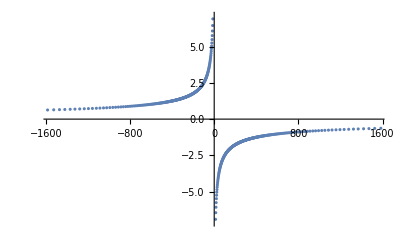

```mathematica
ListPlot[Table[{x[[i]],Im[y[[i]]]},{i,1,n}]]
```

```mathematica
s1={};ynn={};
(*Do[klo=1;khi=n;s=x[[1]]+(x[[n]]-x[[1]])/n*(j-1);s1=AppendTo[s1,s];
While[khi-klo>1,i=Floor[(khi+klo)/2];If[x[[i]]>s,khi=i,klo=i]];
yn=a[[i]]+b[[i]]*(s-x[[i]])+c[[i]]*(s-x[[i]])^2+d[[i]] (s-x[[i]])^3;ynn=AppendTo[ynn,yn],{j,1,300}]*)
Do[klo=1;khi=nn-1;s=Ω[[1]]+(Ω[[nn-1]]-Ω[[1]])/(nn-1)*(j-1);s1=AppendTo[s1,s];
While[khi-klo>1,i=Floor[(khi+klo)/2];If[Ω[[i]]>s,khi=i,klo=i]];
yn=a[[i]]+b[[i]]*(s-Ω[[i]])+c[[i]]*(s-Ω[[i]])^2+d[[i]] (s-Ω[[i]])^3;ynn=AppendTo[ynn,yn],{j,1,298}]
```

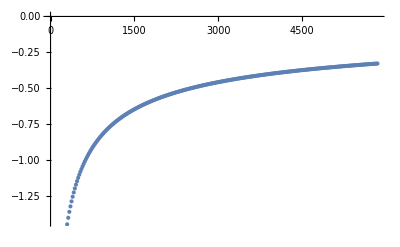

```mathematica
ListPlot[Table[{s1[[i]],Re[ynn[[i]]]},{i,1,298}]]
```

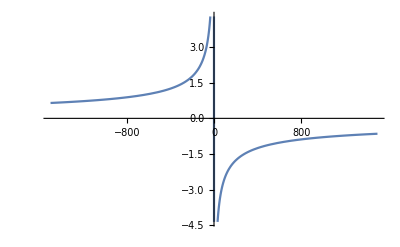

```mathematica
f=Interpolation[Table[{x[[i]],Im[y[[i]]]},{i,1,n}], Method->"Spline"];
Plot[f[kk],{kk,-5000,1500}]
```

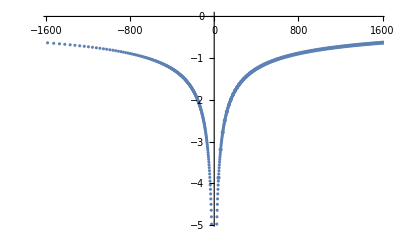

```mathematica
Show[%206,%342]
```

```mathematica
ep[k_]:=k^2- μ;
G[k_,τ_]:=ⅇ^(-ep[k] τ)/(ⅇ^(-β ep[k])+1.);
Manipulate[Plot[Re[G[k[[1]],ττ] ⅇ^(ⅈ ττ ω[[i]])],{ττ,0,β}],{i,1,10,1}]
```

```mathematica
I00[ω_,τ_,j_]:=ⅇ^(ⅈ τ[[j]] ω)((ⅇ^(ⅈ ω (τ[[j+1]]-τ[[j]]))-1)/(ⅈ ω));
I11[ω_,τ_,j_]:=(ⅇ^(ⅈ τ[[j]] ω) (-1+ⅇ^(ⅈ (-τ[[j]]+τ[[j+1]]) ω) (1+ⅈ (τ[[j]]-τ[[j+1]]) ω)))/ω^2;
I22[ω_,τ_,j_]:=1/ω^3 ⅇ^(ⅈ τ[[j+1]] ω) (2 ⅈ-2 ⅈ ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-2-ⅈ (τ[[j]]-τ[[j+1]]) ω));
I33[ω_,τ_,j_]:=1/ω^4 ⅇ^(ⅈ τ[[j+1]] ω) (-6+6 ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-6 ⅈ+(τ[[j]]-τ[[j+1]]) ω (3+ⅈ (τ[[j]]-τ[[j+1]]) ω)));
J00[ω_]:=-ⅈ/ω;
J11[ω_]:=1/ω^2 ;
J22[ω_]:=(2 ⅈ)/ω^3;
J33[ω_]:=-6/ω^4;

ep[k_]:=k^2-4. μ;

x=τ;
y=8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},MaxRecursion->20, AccuracyGoal->8,Method->"PrincipalValue",Exclusions->-ep[k]];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];
Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,1,nn-1}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,1,nn-1}];
c=Table[y2[[i]]/2.,{i,1,nn-1}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,1,nn-1}];

f1=Table[Table[I00[Ω[[j]],τ,i]*a[[i]]+I11[Ω[[j]],τ,i]*b[[i]]+I22[Ω[[j]],τ,i]*c[[i]]+I33[Ω[[j]],τ,i]*d[[i]],{i,1,nn-1}]//Total,{j,1,nn-1}]
```

{-9.40853-19.375 ⅈ,-7.36723-13.3489 ⅈ,-5.81929-10.681 ⅈ,-4.74417-9.12054 ⅈ,-3.95608-8.0667 ⅈ,-3.35003-7.29149 ⅈ,-2.86658-6.68818 ⅈ,-2.46995-6.19954 ⅈ,-2.13737-5.79184 ⅈ,-1.8536-5.44377 ⅈ,-1.60802-5.14113 ⅈ,-1.39301-4.87405 ⅈ,-1.20291-4.63543 ⅈ,-1.03345-4.42 ⅈ,-0.881326-4.22379 ⅈ,-0.743928-4.04371 ⅈ,-0.619181-3.87733 ⅈ,-0.505405-3.72272 ⅈ,-0.401221-3.5783 ⅈ,-0.305484-3.44279 ⅈ,-0.21724-3.31512 ⅈ,-0.135685-3.1944 ⅈ,-0.0601325-3.07987 ⅈ,0.0100062-2.97091 ⅈ,0.0752358-2.86696 ⅈ,0.135995-2.76755 ⅈ,0.192669-2.67227 ⅈ,0.245595-2.58077 ⅈ,0.295068-2.49274 ⅈ,0.34135-2.40789 ⅈ,0.384677-2.326 ⅈ,0.425257-2.24685 ⅈ,0.463274-2.17024 ⅈ,0.498901-2.09601 ⅈ,0.532288-2.024 ⅈ,0.563573-1.95408 ⅈ,0.592879-1.88612 ⅈ,0.620323-1.82001 ⅈ,0.646008-1.75565 ⅈ,0.670028-1.69295 ⅈ,0.692473-1.63183 ⅈ,0.713424-1.57221 ⅈ,0.732953-1.51401 ⅈ,0.751129-1.45718 ⅈ,0.768018-1.40166 ⅈ,0.783678-1.3474 ⅈ,0.798165-1.29434 ⅈ,0.81153-1.24244 ⅈ,0.823824-1.19166 ⅈ,0.835088-1.14196 ⅈ,0.845366-1.0933 ⅈ,0.854698-1.04566 ⅈ,0.863123-0.998992 ⅈ,0.870674-0.953278 ⅈ,0.877386-0.908489 ⅈ,0.883291-0.8646 ⅈ,0.888418-0.821587 ⅈ,0.892795-0.77943 ⅈ,0.89645-0.738109 ⅈ,0.89941-0.697605 ⅈ,0.901697-0.657899 ⅈ,0.903337-0.618977 ⅈ,0.904351-0.58082 ⅈ,0.904761-0.543416 ⅈ,0.904587-0.50675 ⅈ,0.903849-0.470811 ⅈ,0.902567-0.435584 ⅈ,0.900758-0.40106 ⅈ,0.898441-0.367226 ⅈ,0.895632-0.334073 ⅈ,0.892347-0.30159 ⅈ,0.888603-0.269769 ⅈ,0.884415-0.238601 ⅈ,0.879798-0.208077 ⅈ,0.874766-0.17819 ⅈ,0.869333-0.14893 ⅈ,0.863512-0.120292 ⅈ,0.857318-0.0922672 ⅈ,0.850762-0.0648504 ⅈ,0.843857-0.0380346 ⅈ,0.836616-0.0118134 ⅈ,0.82905+0.0138194 ⅈ,0.821171+0.0388697 ⅈ,0.81299+0.0633429 ⅈ,0.804517+0.0872443 ⅈ,0.795765+0.110579 ⅈ,0.786743+0.133353 ⅈ,0.777462+0.15557 ⅈ,0.767931+0.177237 ⅈ,0.758162+0.198357 ⅈ,0.748162+0.218935 ⅈ,0.737943+0.238976 ⅈ,0.727512+0.258484 ⅈ,0.71688+0.277464 ⅈ,0.706055+0.29592 ⅈ,0.695047+0.313857 ⅈ,0.683863+0.331279 ⅈ,0.672512+0.34819 ⅈ,0.661003+0.364594 ⅈ,0.649343+0.380496 ⅈ,0.637542+0.395899 ⅈ,0.625607+0.410808 ⅈ,0.613545+0.425227 ⅈ,0.601364+0.43916 ⅈ,0.589072+0.452611 ⅈ,0.576677+0.465584 ⅈ,0.564185+0.478083 ⅈ,0.551604+0.490113 ⅈ,0.538941+0.501677 ⅈ,0.526203+0.51278 ⅈ,0.513397+0.523426 ⅈ,0.500529+0.533619 ⅈ,0.487606+0.543363 ⅈ,0.474635+0.552661 ⅈ,0.461623+0.56152 ⅈ,0.448575+0.569942 ⅈ,0.435498+0.577931 ⅈ,0.422397+0.585494 ⅈ,0.40928+0.592632 ⅈ,0.396152+0.599351 ⅈ,0.383019+0.605656 ⅈ,0.369887+0.61155 ⅈ,0.356761+0.617038 ⅈ,0.343646+0.622124 ⅈ,0.33055+0.626814 ⅈ,0.317476+0.63111 ⅈ,0.304431+0.635019 ⅈ,0.291419+0.638544 ⅈ,0.278445+0.641691 ⅈ,0.265515+0.644463 ⅈ,0.252634+0.646866 ⅈ,0.239807+0.648904 ⅈ,0.227037+0.650583 ⅈ,0.214331+0.651906 ⅈ,0.201692+0.652878 ⅈ,0.189125+0.653505 ⅈ,0.176635+0.653792 ⅈ,0.164225+0.653742 ⅈ,0.151901+0.653362 ⅈ,0.139666+0.652656 ⅈ,0.127524+0.65163 ⅈ,0.11548+0.650287 ⅈ,0.103537+0.648634 ⅈ,0.0916998+0.646676 ⅈ,0.0799711+0.644417 ⅈ,0.0683548+0.641863 ⅈ,0.0568547+0.639019 ⅈ,0.0454741+0.63589 ⅈ,0.0342166+0.632481 ⅈ,0.0230853+0.628798 ⅈ,0.00121443+0.62063 ⅈ,-0.0201138+0.611429 ⅈ,-0.030567+0.606454 ⅈ,-0.0408759+0.601237 ⅈ,-0.0510378+0.595783 ⅈ,-0.06105+0.590098 ⅈ,-0.07091+0.584186 ⅈ,-0.0806154+0.578054 ⅈ,-0.0901638+0.571707 ⅈ,-0.0995529+0.56515 ⅈ,-0.108781+0.558388 ⅈ,-0.117845+0.551428 ⅈ,-0.135474+0.536934 ⅈ,-0.144035+0.52941 ⅈ,-0.152426+0.52171 ⅈ,-0.160643+0.513839 ⅈ,-0.168686+0.505802 ⅈ,-0.176553+0.497604 ⅈ,-0.184242+0.489252 ⅈ,-0.191753+0.480751 ⅈ,-0.206232+0.463322 ⅈ,-0.213199+0.454405 ⅈ,-0.219983+0.445361 ⅈ,-0.226582+0.436195 ⅈ,-0.232996+0.426912 ⅈ,-0.245265+0.408019 ⅈ,-0.251118+0.398419 ⅈ,-0.256784+0.388725 ⅈ,-0.262262+0.37894 ⅈ,-0.26755+0.369071 ⅈ,-0.27756+0.349102 ⅈ,-0.282281+0.339012 ⅈ,-0.286812+0.328858 ⅈ,-0.295305+0.308382 ⅈ,-0.299268+0.29807 ⅈ,-0.303041+0.287715 ⅈ,-0.310021+0.266897 ⅈ,-0.313229+0.256444 ⅈ,-0.319082+0.235475 ⅈ,-0.321728+0.224968 ⅈ,-0.324188+0.214454 ⅈ,-0.328555+0.19342 ⅈ,-0.330463+0.18291 ⅈ,-0.333734+0.161927 ⅈ,-0.336283+0.141023 ⅈ,-0.33729+0.130612 ⅈ,-0.338777+0.109895 ⅈ,-0.339258+0.0995975 ⅈ,-0.339706+0.0791446 ⅈ,-0.339477+0.0589094 ⅈ,-0.338583+0.0389242 ⅈ,-0.337039+0.0192203 ⅈ,-0.336028+0.00948324 ⅈ,-0.333537-0.00974246 ⅈ,-0.330435-0.0286132 ⅈ,-0.326738-0.0471015 ⅈ,-0.322463-0.0651808 ⅈ,-0.315007-0.0914775 ⅈ,-0.309369-0.108426 ⅈ,-0.303218-0.124881 ⅈ,-0.296576-0.140822 ⅈ,-0.285736-0.163725 ⅈ,-0.277956-0.178295 ⅈ,-0.265508-0.199058 ⅈ,-0.252194-0.218466 ⅈ,-0.242875-0.230629 ⅈ,-0.228286-0.247678 ⅈ,-0.213037-0.263262 ⅈ,-0.197204-0.277353 ⅈ,-0.180868-0.289927 ⅈ,-0.158437-0.304306 ⅈ,-0.141231-0.313287 ⅈ,-0.117926-0.322856 ⅈ,-0.100276-0.328232 ⅈ,-0.0766567-0.333024 ⅈ,-0.0531017-0.335139 ⅈ,-0.0297816-0.334636 ⅈ,-0.0012119-0.330446 ⅈ,0.0209891-0.324358 ⅈ,0.0476809-0.313508 ⅈ,0.0729473-0.299285 ⅈ,0.0965454-0.281961 ⅈ,0.118258-0.261832 ⅈ,0.14156-0.234423 ⅈ,0.161603-0.204015 ⅈ,0.178175-0.171213 ⅈ,0.191127-0.136643 ⅈ,0.20155-0.0949129 ⅈ,0.2069-0.0526236 ⅈ,0.207254-0.0107402 ⅈ,0.201785+0.0354521 ⅈ,0.190466+0.0786443 ⅈ,0.173876+0.117704 ⅈ,0.149792+0.155505 ⅈ,0.121081+0.185754 ⅈ,0.0853003+0.209565 ⅈ,0.0472067+0.222503 ⅈ,0.00483606+0.224097 ⅈ,-0.0357346+0.213024 ⅈ,-0.0754213+0.187957 ⅈ,-0.108055+0.151631 ⅈ,-0.133396+0.102999 ⅈ,-0.147521+0.0445988 ⅈ,-0.147531-0.0146451 ⅈ,-0.132771-0.0730381 ⅈ,-0.102846-0.123338 ⅈ,-0.0625387-0.156299 ⅈ,-0.0113529-0.169224 ⅈ,0.0384265-0.156374 ⅈ,0.083387-0.116132 ⅈ,0.110371-0.0573481 ⅈ,0.115327+0.0115029 ⅈ,0.0940967+0.0789199 ⅈ,0.0496625+0.124359 ⅈ,-0.00470869+0.134629 ⅈ,-0.0596035+0.104081 ⅈ,-0.0913335+0.0418411 ⅈ,-0.0899451-0.0348558 ⅈ,-0.0517869-0.0960141 ⅈ,0.00749314-0.111841 ⅈ,0.061609-0.072624 ⅈ,0.0804521+0.00495919 ⅈ,0.049998+0.0767642 ⅈ,-0.0109296+0.0950375 ⅈ,-0.0624607+0.044487 ⅈ,-0.0618496-0.0390261 ⅈ,-0.00642438-0.0847325 ⅈ,0.0521063-0.0458208 ⅈ,0.0529441+0.0385158 ⅈ,-0.00660352+0.0745447 ⅈ,-0.0546125+0.0135362 ⅈ,-0.0236181-0.0618778 ⅈ,0.0403914-0.0401149 ⅈ,0.0340421+0.0454591 ⅈ,-0.032686+0.0429624 ⅈ,-0.0306766-0.0421396 ⅈ,0.0350636-0.0313363 ⅈ,0.0156784+0.0487639 ⅈ,-0.0389105+0.00343216 ⅈ,0.013112-0.0449746 ⅈ,0.0221139+0.0360536 ⅈ,-0.0339332+0.000850617 ⅈ,0.0222342-0.0303184 ⅈ,-0.00228642+0.0397781 ⅈ,-0.0129839-0.0341883 ⅈ,0.0212203+0.0238258 ⅈ,-0.0239095-0.0156198 ⅈ,0.0237767+0.012011 ⅈ,-0.0218911-0.0136956 ⅈ}

```mathematica
(16.π)/(2. η-√(ep[k[[1]]]-2 ⅈ Ω))
```

{-13.2073-19.4059 ⅈ,-11.1655-13.4109 ⅈ,-9.61676-10.774 ⅈ,-8.54048-9.24443 ⅈ,-7.75092-8.22151 ⅈ,-7.14307-7.4772 ⅈ,-6.65749-6.90475 ⅈ,-6.25841-6.44692 ⅈ,-5.92305-6.06998 ⅈ,-5.63617-5.75262 ⅈ,-5.38716-5.48062 ⅈ,-5.1684-5.24412 ⅈ,-4.97423-5.036 ⅈ,-4.80037-4.85099 ⅈ,-4.64353-4.68511 ⅈ,-4.5011-4.53526 ⅈ,-4.371-4.39902 ⅈ,-4.25155-4.27445 ⅈ,-4.14139-4.15995 ⅈ,-4.03936-4.05425 ⅈ,-3.94451-3.95626 ⅈ,-3.85603-3.86509 ⅈ,-3.77326-3.77999 ⅈ,-3.69559-3.70031 ⅈ,-3.62253-3.62549 ⅈ,-3.55363-3.55506 ⅈ,-3.48852-3.4886 ⅈ,-3.42686-3.42576 ⅈ,-3.36836-3.36621 ⅈ,-3.31275-3.30969 ⅈ,-3.25981-3.25593 ⅈ,-3.20933-3.20472 ⅈ,-3.16112-3.15588 ⅈ,-3.11502-3.10921 ⅈ,-3.07088-3.06456 ⅈ,-3.02857-3.02179 ⅈ,-2.98795-2.98077 ⅈ,-2.94893-2.94139 ⅈ,-2.9114-2.90354 ⅈ,-2.87526-2.86712 ⅈ,-2.84044-2.83204 ⅈ,-2.80685-2.79822 ⅈ,-2.77443-2.7656 ⅈ,-2.74311-2.73409 ⅈ,-2.71282-2.70365 ⅈ,-2.68351-2.6742 ⅈ,-2.65514-2.6457 ⅈ,-2.62764-2.61809 ⅈ,-2.60098-2.59134 ⅈ,-2.57512-2.56539 ⅈ,-2.55001-2.54022 ⅈ,-2.52563-2.51577 ⅈ,-2.50193-2.49201 ⅈ,-2.47888-2.46892 ⅈ,-2.45646-2.44647 ⅈ,-2.43464-2.42462 ⅈ,-2.41339-2.40334 ⅈ,-2.39268-2.38262 ⅈ,-2.3725-2.36243 ⅈ,-2.35283-2.34274 ⅈ,-2.33363-2.32354 ⅈ,-2.31489-2.30481 ⅈ,-2.2966-2.28653 ⅈ,-2.27874-2.26867 ⅈ,-2.26129-2.25123 ⅈ,-2.24423-2.23419 ⅈ,-2.22755-2.21753 ⅈ,-2.21124-2.20123 ⅈ,-2.19528-2.1853 ⅈ,-2.17967-2.1697 ⅈ,-2.16438-2.15444 ⅈ,-2.14941-2.1395 ⅈ,-2.13474-2.12486 ⅈ,-2.12037-2.11052 ⅈ,-2.10629-2.09647 ⅈ,-2.09248-2.08269 ⅈ,-2.07895-2.06919 ⅈ,-2.06567-2.05595 ⅈ,-2.05264-2.04295 ⅈ,-2.03986-2.0302 ⅈ,-2.02731-2.01769 ⅈ,-2.01499-2.00541 ⅈ,-2.00289-1.99335 ⅈ,-1.99101-1.98151 ⅈ,-1.97934-1.96987 ⅈ,-1.96787-1.95844 ⅈ,-1.95659-1.94721 ⅈ,-1.94551-1.93617 ⅈ,-1.93462-1.92531 ⅈ,-1.9239-1.91464 ⅈ,-1.91336-1.90414 ⅈ,-1.903-1.89381 ⅈ,-1.8928-1.88365 ⅈ,-1.88276-1.87365 ⅈ,-1.87288-1.86381 ⅈ,-1.86315-1.85413 ⅈ,-1.85358-1.84459 ⅈ,-1.84415-1.8352 ⅈ,-1.83486-1.82596 ⅈ,-1.82571-1.81685 ⅈ,-1.8167-1.80787 ⅈ,-1.80782-1.79903 ⅈ,-1.79907-1.79032 ⅈ,-1.79044-1.78174 ⅈ,-1.78194-1.77327 ⅈ,-1.77355-1.76493 ⅈ,-1.76529-1.7567 ⅈ,-1.75714-1.74859 ⅈ,-1.7491-1.74059 ⅈ,-1.74117-1.7327 ⅈ,-1.73334-1.72491 ⅈ,-1.72563-1.71723 ⅈ,-1.71801-1.70966 ⅈ,-1.71049-1.70218 ⅈ,-1.70307-1.6948 ⅈ,-1.69575-1.68751 ⅈ,-1.68852-1.68032 ⅈ,-1.68138-1.67322 ⅈ,-1.67434-1.66621 ⅈ,-1.66738-1.65928 ⅈ,-1.6605-1.65245 ⅈ,-1.65371-1.64569 ⅈ,-1.64701-1.63902 ⅈ,-1.64038-1.63243 ⅈ,-1.63383-1.62592 ⅈ,-1.62736-1.61949 ⅈ,-1.62097-1.61313 ⅈ,-1.61465-1.60685 ⅈ,-1.60841-1.60064 ⅈ,-1.60224-1.5945 ⅈ,-1.59613-1.58843 ⅈ,-1.5901-1.58243 ⅈ,-1.58414-1.5765 ⅈ,-1.57824-1.57063 ⅈ,-1.5724-1.56483 ⅈ,-1.56663-1.5591 ⅈ,-1.56093-1.55343 ⅈ,-1.55528-1.54781 ⅈ,-1.5497-1.54226 ⅈ,-1.54418-1.53677 ⅈ,-1.53871-1.53134 ⅈ,-1.53331-1.52596 ⅈ,-1.52796-1.52064 ⅈ,-1.52266-1.51538 ⅈ,-1.51742-1.51017 ⅈ,-1.51223-1.50501 ⅈ,-1.5071-1.49991 ⅈ,-1.50202-1.49486 ⅈ,-1.49699-1.48986 ⅈ,-1.49201-1.48491 ⅈ,-1.48219-1.47515 ⅈ,-1.47257-1.46559 ⅈ,-1.46783-1.46088 ⅈ,-1.46313-1.45621 ⅈ,-1.45848-1.45158 ⅈ,-1.45387-1.44701 ⅈ,-1.44931-1.44247 ⅈ,-1.44479-1.43798 ⅈ,-1.44031-1.43352 ⅈ,-1.43587-1.42911 ⅈ,-1.43148-1.42474 ⅈ,-1.42712-1.42041 ⅈ,-1.41852-1.41187 ⅈ,-1.41428-1.40766 ⅈ,-1.41008-1.40348 ⅈ,-1.40592-1.39934 ⅈ,-1.40179-1.39524 ⅈ,-1.3977-1.39117 ⅈ,-1.39364-1.38714 ⅈ,-1.38962-1.38315 ⅈ,-1.38168-1.37526 ⅈ,-1.37776-1.37136 ⅈ,-1.37387-1.3675 ⅈ,-1.37002-1.36367 ⅈ,-1.3662-1.35988 ⅈ,-1.35865-1.35238 ⅈ,-1.35493-1.34867 ⅈ,-1.35123-1.345 ⅈ,-1.34756-1.34136 ⅈ,-1.34393-1.33774 ⅈ,-1.33674-1.3306 ⅈ,-1.33319-1.32708 ⅈ,-1.32967-1.32358 ⅈ,-1.32271-1.31666 ⅈ,-1.31927-1.31324 ⅈ,-1.31586-1.30985 ⅈ,-1.30911-1.30315 ⅈ,-1.30578-1.29984 ⅈ,-1.29918-1.29328 ⅈ,-1.29592-1.29005 ⅈ,-1.29269-1.28683 ⅈ,-1.28629-1.28047 ⅈ,-1.28313-1.27733 ⅈ,-1.27687-1.27111 ⅈ,-1.2707-1.26498 ⅈ,-1.26765-1.26195 ⅈ,-1.26161-1.25596 ⅈ,-1.25863-1.25299 ⅈ,-1.25272-1.24712 ⅈ,-1.2469-1.24133 ⅈ,-1.24115-1.23562 ⅈ,-1.23548-1.22999 ⅈ,-1.23268-1.22721 ⅈ,-1.22713-1.22169 ⅈ,-1.22165-1.21625 ⅈ,-1.21625-1.21088 ⅈ,-1.21091-1.20558 ⅈ,-1.20304-1.19776 ⅈ,-1.19788-1.19263 ⅈ,-1.19278-1.18757 ⅈ,-1.18775-1.18257 ⅈ,-1.18032-1.17519 ⅈ,-1.17544-1.17034 ⅈ,-1.16824-1.16319 ⅈ,-1.16117-1.15616 ⅈ,-1.15652-1.15155 ⅈ,-1.14966-1.14473 ⅈ,-1.14292-1.13803 ⅈ,-1.13629-1.13145 ⅈ,-1.12978-1.12498 ⅈ,-1.12127-1.11652 ⅈ,-1.11502-1.11031 ⅈ,-1.10683-1.10218 ⅈ,-1.10081-1.0962 ⅈ,-1.09294-1.08837 ⅈ,-1.08523-1.08071 ⅈ,-1.07768-1.07321 ⅈ,-1.06846-1.06405 ⅈ,-1.06125-1.05689 ⅈ,-1.05245-1.04814 ⅈ,-1.04386-1.03961 ⅈ,-1.03547-1.03128 ⅈ,-1.02729-1.02315 ⅈ,-1.01772-1.01364 ⅈ,-1.00841-1.00439 ⅈ,-0.999355-0.995388 ⅈ,-0.990537-0.986627 ⅈ,-0.98054-0.976693 ⅈ,-0.970839-0.967053 ⅈ,-0.961421-0.957694 ⅈ,-0.950985-0.947324 ⅈ,-0.940883-0.937285 ⅈ,-0.931095-0.927558 ⅈ,-0.920441-0.91697 ⅈ,-0.910145-0.906737 ⅈ,-0.8991-0.895761 ⅈ,-0.888447-0.885173 ⅈ,-0.877156-0.873951 ⅈ,-0.866285-0.863146 ⅈ,-0.854874-0.851804 ⅈ,-0.843903-0.840899 ⅈ,-0.832481-0.829545 ⅈ,-0.820685-0.817819 ⅈ,-0.809377-0.806577 ⅈ,-0.797765-0.795033 ⅈ,-0.785913-0.783251 ⅈ,-0.774575-0.771977 ⅈ,-0.762387-0.75986 ⅈ,-0.750758-0.748296 ⅈ,-0.73844-0.736048 ⅈ,-0.726709-0.724383 ⅈ,-0.714975-0.712713 ⅈ,-0.702753-0.700558 ⅈ,-0.690645-0.688516 ⅈ,-0.679142-0.677075 ⅈ,-0.666863-0.664862 ⅈ,-0.655228-0.653288 ⅈ,-0.643385-0.641506 ⅈ,-0.631409-0.629592 ⅈ,-0.619722-0.617965 ⅈ,-0.60799-0.606291 ⅈ,-0.596266-0.594626 ⅈ,-0.584598-0.583015 ⅈ,-0.573307-0.571779 ⅈ,-0.561851-0.560378 ⅈ,-0.550557-0.549137 ⅈ,-0.539215-0.537847 ⅈ,-0.528105-0.526788 ⅈ,-0.517242-0.515974 ⅈ,-0.50644-0.50522 ⅈ,-0.49556-0.494388 ⅈ,-0.485012-0.483885 ⅈ,-0.47463-0.473547 ⅈ,-0.464289-0.463249 ⅈ,-0.454036-0.453038 ⅈ,-0.444042-0.443084 ⅈ,-0.434068-0.43315 ⅈ,-0.424395-0.423514 ⅈ,-0.414807-0.413963 ⅈ,-0.405344-0.404535 ⅈ,-0.396035-0.395261 ⅈ,-0.386907-0.386167 ⅈ,-0.377899-0.37719 ⅈ,-0.369116-0.368438 ⅈ,-0.360428-0.359779 ⅈ,-0.351935-0.351315 ⅈ,-0.343591-0.342999 ⅈ,-0.335419-0.334853 ⅈ,-0.327384-0.326843 ⅈ,-3.48446+35.1982 ⅈ}

```mathematica
f[τ_?NumericQ]:=8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},Method->"PrincipalValue",Exclusions->-ep[k]]
NIntegrate[f[ττ]*ⅇ^(ⅈ ττ Ω),{ττ,0,β},MaxRecursion->20, AccuracyGoal->8]
```

$Aborted

```mathematica
ListPlot[Table[{x[[i]],y[[i]]},{i,1,n}]]
```